```mathematica
Clear["Global`*"]
Needs["ErrorBarPlots`"]
SetDirectory[NotebookDirectory[]];
```

```mathematica
rawDataRR=Import["rrTrace.txt","Table"];
npart = rawDataRR[[2,1]];
nd = rawDataRR[[2,2]];
βRR = rawDataRR[[2,3]];
ωRR = rawDataRR[[2,4]];
nbead = rawDataRR[[2,5]];
datasRR = Table[rawDataRR[[n]],{n,3,Length[rawDataRR]}];
```

```mathematica
For[i=1,i<=nbead,i++,dataRR[i]=Table[datasRR[[n,i]],{n,1,Length[datasRR]}]];
For[i=1,i<=nbead,i++,stdErrRR[i] = StandardDeviation[dataRR[i]]/√Length[dataRR[i]]]
```

```mathematica
pointsRR=Table[{{i-1,Mean[dataRR[i]]},ErrorBar[stdErrRR[i]]},{i,1,nbead}];
```

```mathematica
c0[j_,β_,ω_,d_,τ_]:=(d ℏ)/(2m ω)(Cosh[(β ℏ ω)/2-τ j ω]/Sinh[(β ℏ ω)/2]);
Z0[β_,ω_,d_]:=(1/(2 Sinh[(β ℏ ω)/2]))^d;
z2[β_,ω_,d_]:=1/2(Z0[β,ω,d]^2-Z0[2β,ω,d]);
c2[j_,β_,ω_,d_,τ_]:=1/z2[β,ω,d](Z0[β,ω,d]^2 c0[j,β,ω,d,τ]-Z0[2β,ω,d]c0[j,2β,ω,d,2τ]);
```

```mathematica
c2[j,β,ω,d,τ]
```

(2 ((2^(-1-2 d) d ℏ Cosh[j τ ω-(β ω ℏ)/2] Csch[(β ω ℏ)/2]^(1+2 d))/(m ω)-(2^(-1-d) d ℏ Cosh[2 j τ ω-β ω ℏ] Csch[β ω ℏ]^(1+d))/(m ω)))/(2^(-2 d) Csch[(β ω ℏ)/2]^(2 d)-2^-d Csch[β ω ℏ]^d)

```mathematica
FullSimplify[TrigExpand[c2[j,β,ω,d,τ]]]
```

(d ℏ Csch[β ω ℏ] ((Cosh[j τ ω]+Cosh[ω (j τ-β ℏ)]) Csch[(β ω ℏ)/2]^(2 d)-2^d Cosh[ω (2 j τ-β ℏ)] Csch[β ω ℏ]^d))/(m ω (Csch[(β ω ℏ)/2]^(2 d)-2^d Csch[β ω ℏ]^d))

```mathematica
(d ℏ Csch[β ω ℏ] (Cosh[ω (j τ-β ℏ)]+Cosh[j τ ω]/(1-2^d Csch[(β ω ℏ)/2]^(-2 d) Csch[β ω ℏ]^d)))/(m ω)
```

(d ℏ Csch[β ω ℏ] (Cosh[ω (j τ-β ℏ)]+Cosh[j τ ω]/(1-2^d Csch[(β ω ℏ)/2]^(-2 d) Csch[β ω ℏ]^d)))/(m ω)

```mathematica
c2b[j_,β_,ω_,d_,τ_]:=(d ℏ Csch[β ω ℏ] (Cosh[ω (j τ-β ℏ)]+Cosh[j τ ω]/(1-(Tanh[(β ℏ ω)/2])^d)))/(m ω);
```

```mathematica
FullSimplify[c2b[0,β,ω,2,τ]]
```

(ℏ (3 Coth[β ω ℏ]+Csch[β ω ℏ]))/(m ω)

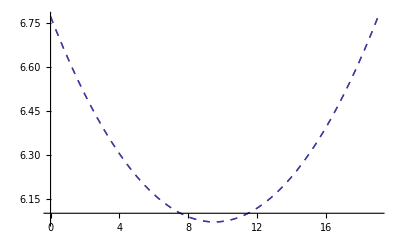

```mathematica
modelRRPlot=Plot[c2[j,1,1,3,1/20]/.{ℏ-> 1,m-> 1},{j,0,19},PlotStyle->Dashed];
modelRRPlotb=Plot[c2b[j,1,1,3,1/20]/.{ℏ-> 1,m-> 1},{j,0,19},PlotStyle->Dashed];
Show[modelRRPlotb,modelRRPlot]
```

```mathematica
￿￿
```

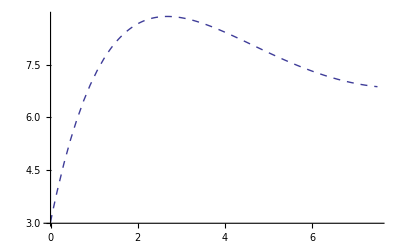

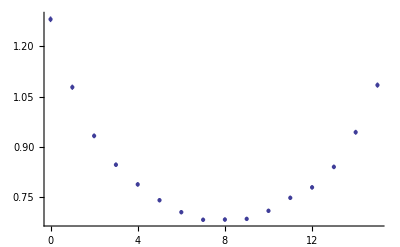

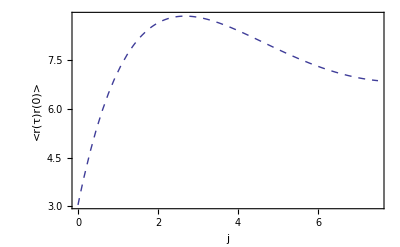

```mathematica
modelRRPlot=Plot[c2[j,βRR,ωRR,nd,βRR/nbead]/.{ℏ-> 1,m-> 1},{j,0,(nbead-1)/2},PlotStyle->Dashed]
pointsRRPlot=ErrorListPlot[pointsRR,PlotStyle->Thick]
Show[modelRRPlot,pointsRRPlot,LabelStyle->Directive[FontFamily->"Helvetica"],Frame->True,FrameLabel-> {Style["j",Bold],Style["<r(τ)r(0)>",Bold]}]
```